# Converting Yasasya’s Files

There are two matrix files from in this directory that are not in a particularly portable form.  I should really convert them to the portable “mtx” form we looked at. Instead I am just going to read work out how to read them into Mathematica: I want to understand what they look like.

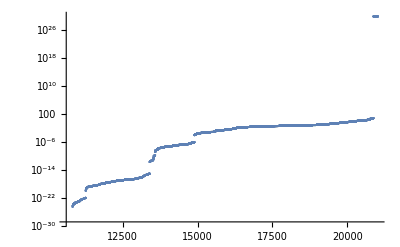

SparseArray[<10199>, {410, 410}]

SparseArray[<10199>, {410, 410}]

Matrix1.txt

```mathematica
SetDirectory["C:\\Users\\struther\\Desktop\\2022-23-Classes\\5631\\SampleMatrices"];
fStream=OpenRead["Matrix1.txt"];
Skip[fStream,"String",2]
{n,m,nz}=Read[fStream,{Number,Number,Number}];
Skip[fStream,"String"];
A1 = Partition[ReadList[fStream,Number],3]/.{i_,j_,z_}:>{i+1,j+1}->z;
ListLogPlot[Sort[Abs[A1⟦All,2⟧]],PlotRange->All]
A1F=Select[A1, Abs[#⟦2⟧]>0 &];
A1=SparseArray[A1,{n,m}]
A1F=SparseArray[A1F]
Close[fStream]
```

```mathematica
A1⟦All,
```

SparseArray[<10199>, {410, 410}]

SparseArray[<10199>, {410, 410}]

Matrix1.txt

```mathematica
A1[[1]]
```

```mathematica
Head[1.0000000000000000199`19.*^30]
```

Real

```mathematica
{404,404}->1.0000000000000000199`19.*^30
```

```mathematica
SparseArray[A1,{n,m}]
```

SparseArray::posd: The left-hand side of {0,0}→1.00000000000000002×10^30 in {{404,404}→1.00000000000000002×10^30,{404,380}→-0.004256111111111118492,{404,398}→-0.0000894444444444509614,{404,394}→-0.0361111111111111216,{404,390}→-0.03575333333333333141,{404,386}→-0.02741999999999999993,{404,405}→0,{404,381}→0,{404,399}→0,{404,395}→0,«21010»} is not a position or a pattern that will match the position of an element in an array with dimensions {410,410}.

SparseArray[{{404,404}→1.00000000000000002×10^30,{404,380}→-0.004256111111111118492,{404,398}→-0.0000894444444444509614,{404,394}→-0.0361111111111111216,{404,390}→-0.03575333333333333141,21010,{237,263}→0.04166666649592422334,{287,256}→0,{287,257}→0,{287,258}→-0.02777777786314900022,{287,259}→-0.02777777769240655573},{410,410}]
 |  |  |  |

SparseArray[{{404,404}→1.00000000000000002×10^30,{404,380}→-0.004256111111111118492,{404,398}→-0.0000894444444444509614,{404,394}→-0.0361111111111111216,{404,390}→-0.03575333333333333141,{404,386}→-0.02741999999999999993,21009,{237,263}→0.04166666649592422334,{287,256}→0,{287,257}→0,{287,258}→-0.02777777786314900022,{287,259}→-0.02777777769240655573}]
 |  |  |  |

{0,fortran half m n nnz state #1,0,30+163216.0000000000032 e,153519.995743888888888881508,160787-8.94444444444509614 e,159175.9638888888888888784,157559.96424666666666666859,21007,0,0,-11+530104.1799360187568 e,2597.124989357452765,0,0,74045.97222222213685099979,74332.97222222230759344427}
 |  |  |  |

```mathematica
?Skip
```

We need to read in all the numbers (ignoring the parenthesis) and fix the zero based counting then build the Mma sparse structure. To convert to mtx we also need to count the number of entries, write out the mtx header, and all the entries (in the mtx format), and zero based reference to the linear algebra based mtx format.

Building a Mathematica matrix

```mathematica
SetDirectory["C:\\Users\\struther\\Desktop\\2022-23-Classes\\5631\\SampleMatrices\\Week2_Kyle"];MessyData=ReadList["allTerms.txt",{Character,Number,Character,Number,Character,Real,Character}];
ZeroBaseData=MessyData⟦All,{2,4,6}⟧;
nz=Length[ZeroBaseData];
A=SparseArray[Table[
{i,j,a}=ZeroBaseData⟦k⟧+{1,1,0.0};
{i,j}->a,
{k, nz}]]
{m1,m2}={3500,4500};
TabView[{
"A"->MatrixPlot[A,PlotLegends->Automatic],
span=Span[m1,m2];
"CloseUp"->MatrixPlot[A⟦span,span⟧,PlotLegends->Automatic,PlotLabel->StringForm["``:``",m1,m2],
DataRange->{{m1,m2},{m1,m2}}]
}]
```

SparseArray[<1254975>, {9075, 9075}]

12